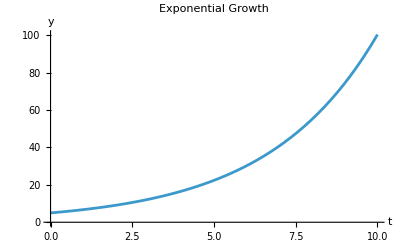

```mathematica
k = 0.3;

sol = DSolve[{y'[t] == k y[t], y[0] == 5}, y[t], t];

Plot[Evaluate[y[t] /. sol], {t, 0, 10},
 PlotLabel -> "Exponential Growth",
 AxesLabel -> {"t", "y"}]
```

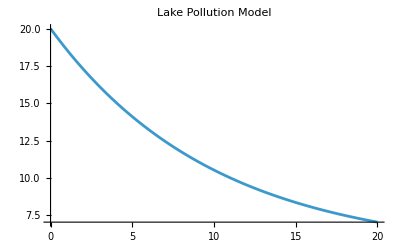

```mathematica
qin = 10; qout = 10; cin = 5;

sol = DSolve[{x'[t] == (qin cin - qout x[t])/100, x[0] == 20}, x[t], t];

Plot[Evaluate[x[t] /. sol], {t, 0, 20},
 PlotLabel -> "Lake Pollution Model"]
```

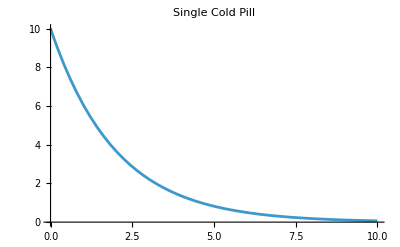

```mathematica
k = 0.5;

sol = DSolve[{c'[t] == -k c[t], c[0] == 10}, c[t], t];

Plot[Evaluate[c[t] /. sol], {t, 0, 10},
 PlotLabel -> "Single Cold Pill"]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

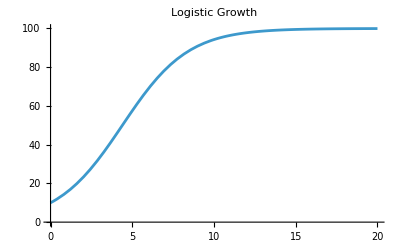

```mathematica
r = 0.5; K = 100;

sol = DSolve[{p'[t] == r p[t] (1 - p[t]/K), p[0] == 10}, p[t], t];

Plot[Evaluate[p[t] /. sol], {t, 0, 20},
 PlotLabel -> "Logistic Growth"]
```

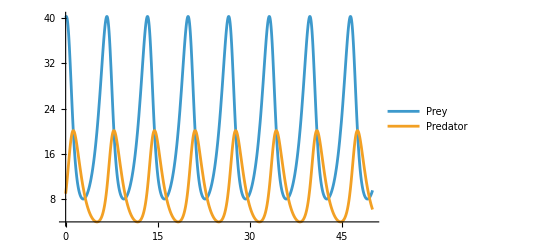

```mathematica
sol = NDSolve[
  {
   x'[t] == x[t] (1 - 0.1 y[t]),
   y'[t] == -y[t] + 0.05 x[t] y[t],
   x[0] == 40, y[0] == 9
   },
  {x, y}, {t, 0, 50}
];

Plot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 50},
 PlotLegends -> {"Prey", "Predator"}]
```

```mathematica
sol = NDSolve[
  {
   s'[t] == -0.002 s[t] i[t],
   i'[t] == 0.002 s[t] i[t] - 0.5 i[t],
   r'[t] == 0.5 i[t],
   s[0] == 990, i[0] == 10, r[0] == 0
   },
  {s, i, r}, {t, 0, 50}
];

Plot[Evaluate[{s[t], i[t], r[t]} /. sol], {t, 0, 50},
 PlotLegends -> {"Susceptible", "Infected", "Recovered"}]
```

NDSolve::ndode: The equations {0.5[0]==0} are not differential equations or initial conditions in the dependent variables {i,s}.

ReplaceAll::reps: {NDSolve[{s'[t]==-0.002 i[t] s[t],i'[t]==-0.5 i[t]+0.002 i[t] s[t],0==0.5 i[t],s[0]==990,i[0]==10,0.5[0]==0},{s,i,0.5},{t,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{s'[0.00102143]==-0.002 i[0.00102143] s[0.00102143],i'[0.00102143]==-0.5 i[0.00102143]+0.002 i[0.00102143] s[0.00102143],0==0.5 i[0.00102143],s[0]==990,i[0]==10,0.5[0]==0},{s,i,0.5},{0.00102143,0,50}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00102143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{s'[0.00102143]==-0.002 i[0.00102143] s[0.00102143],i'[0.00102143]==-0.5 i[0.00102143]+0.002 i[0.00102143] s[0.00102143],0.==0.5 i[0.00102143],s[0.]==990.,i[0.]==10.,0.5[0.]==0.},{s,i,0.5},{0.00102143,0.,50.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 1.02143 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

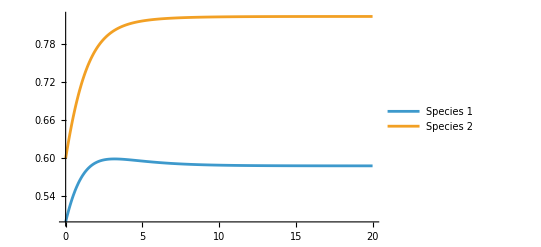

```mathematica
sol = NDSolve[
  {
   x'[t] == x[t] (1 - x[t] - 0.5 y[t]),
   y'[t] == y[t] (1 - y[t] - 0.3 x[t]),
   x[0] == 0.5, y[0] == 0.6
   },
  {x, y}, {t, 0, 20}
];

Plot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 20},
 PlotLegends -> {"Species 1", "Species 2"}]
```

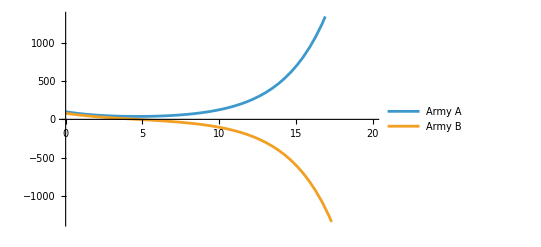

```mathematica
sol = NDSolve[
  {
   x'[t] == -0.4 y[t],
   y'[t] == -0.3 x[t],
   x[0] == 100, y[0] == 80
   },
  {x, y}, {t, 0, 20}
];

Plot[Evaluate[{x[t], y[t]} /. sol], {t, 0, 20},
 PlotLegends -> {"Army A", "Army B"}]
```

```mathematica
pts = RandomReal[{0, 1}, {10000, 2}];

inside = Count[pts, {x_, y_} /; y ≤ x^2];

area = inside/10000
```

1737/5000

```mathematica
data = {{1, 2}, {2, 5}, {3, 10}, {4, 17}};

model = Fit[data, {1, x, x^2}, x]
```

1.+2.83536×10^-15 x+1. x^2

```mathematica
data = {{1, 2}, {2, 8}, {3, 18}, {4, 32}};

FindFit[data, a x^n, {a, n}, x]
```

{a→2.,n→2.}

```mathematica
FindFit[data, b x^n, {b, n}, x]
FindFit[data, b Exp[a x], {a, b}, x]
FindFit[data, a Log[x] + b, {a, b}, x]
FindFit[data, a x^2, {a}, x]
FindFit[data, a x^3, {a}, x]
```

{b→1.52769,n→1.73248}

{a→0.61496,b→1.4732}

{a→10.1506,b→0.435176}

{a→1.08475}

{a→0.286299}